# Costruziazioni proposte dal dott. prof. Fassò™

## Sezione a.

```mathematica
f[μ_,x_]:=μ x(1-x)
```

```mathematica
orbita[μ_,x_,n_]:=NestList[f[μ,#]&,x,n]
```

```mathematica
graficoOrbita[μ_,x_,n_]:=Module[
{
pts=Table[{ξ,ξ},{ξ,NestList[f[μ,#]&,x,n]}]
},
Plot[{f[μ,t],t},{t,Min[x,0],Max[x,1]},PlotStyle->{{Black}},AspectRatio->Automatic,PlotRange->All,Epilog->{{Blue,Thin,Line[{First[#],{First[First@#],Last[Last@#]},Last[#]}]&/@Partition[pts,2,1]},{Red,Thick,Point/@Drop[pts,-1]},{Cyan,Thick,Point[pts//Last]}}]]
```

```mathematica
Manipulate[graficoOrbita[0.1,-0.1,n],{n,Range[25]},Initialization:>{f[μ_,x_]:=μ x(1-x),graficoOrbita[μ_,x_,n_]:=Module[
{
pts=Table[{ξ,ξ},{ξ,NestList[f[μ,#]&,x,n]}]
},
Plot[{f[μ,t],t},{t,Min[x,0],Max[x,1]},PlotStyle->{{Black}},AspectRatio->Automatic,PlotRange->All,Epilog->{{Blue,Thin,Line[{First[#],{First[First@#],Last[Last@#]},Last[#]}]&/@Partition[pts,2,1]},{Red,Thick,Point/@Drop[pts,-1]},{Cyan,Thick,Point[pts//Last]}}]]}]
```

## Sezione b.

Dimostriamo la prima proposizione.

Fissato μ>0, dobbiamo risolvere l’equazione

x=μ x (1-x)

e possiamo risolverla con Mathematica

```mathematica
Solve[{μ>0,x==f[μ,x]},x,Reals]
```

{{x→ConditionalExpression[0, 0<μ<1||μ>1]},{x→ConditionalExpression[(-1+μ)/μ, 0<μ<1||μ>1]}}

La soluzione offerta da Mathematica tralascia il caso μ=1, che però si risolve facilmente perché l’unico punto fisso (con molteplicità doppia) è x=0.

```mathematica
Solve[x==f[1,x],x,Reals]
```

{{x→0},{x→0}}

Vediamo innanzitutto il caso x_0<0:

```mathematica
Reduce[{f[μ,x0]<x0,μ>0,x0<0},x0,Reals]
```

(0<μ≤1&&x0<(-1+μ)/μ)||(μ>1&&x0<0)

Si vede, dunque, che la successione f_μ^n(x_0) è monotona decrescente, a parte in un pezzetto in culo al prof; poiché l’immagine di una parabola concava non è inferiormente limitata, deduciamo che lim_(n→∞) f_μ^n(x_0)=-∞.

Passiamo al caso x_0>1:

```mathematica
Reduce[{f[μ,x0]<x0,μ>0,x0>1},x0,Reals]
```

μ>0&&x0>1

Ottenendo un risultato del tutto simile a quello precedente.

Dimostriamo la seconda proposizione.

Vediamo che

```mathematica
Reduce[{0≤x≤1,0≤f[μ,x]≤1,0<μ≤4},x]
```

0<μ≤4&&0≤x≤1

Vediamo che esiste un intorno di 1/2 che ha orbita divergente.

```mathematica
Reduce[{0≤x≤1,μ>4,0≤f[μ,x]≤1},x]
```

μ>4&&(0≤x≤1/2-1/2 √((-4+μ)/μ)||1/2+1/2 √((-4+μ)/μ)≤x≤1)

## Sezione c.

Creiamo un visualizzatore stupido del punto attrattivo in funzione di μ.

```mathematica
attrattivoPlot[nx_,n_,η_]:=With[{f=Compile[{{μ,_Real},{x,_Real}},μ x(1.-x)]},
ListPlot[
Union@Flatten[Table[
ParallelTable[
{μ,FixedPoint[Chop[f[μ,#]]&,x0,n]},{μ,Subdivide[0,4.,η]}],
{x0,Subdivide[0,1.,nx]}
],1],
PlotStyle->{Thin,Black},
PlotRange->{{0,4},{0,1}},
Ticks->{Subdivide[0,4.,20],Subdivide[0,1.,10]}
]
]
```

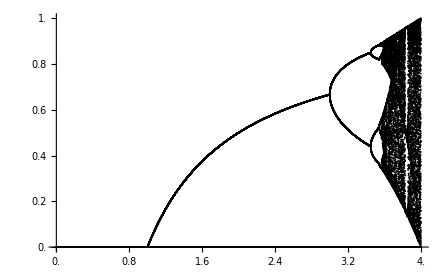

```mathematica
attrattivoPlot[15,10^4,10^4]
```